```mathematica
gCoeff=((2n+1)/n)^n;
eta1=(((2(2n+1)^2)/((3n+2)n^3) ) (R/gCoeff)-cott/n);
eta3=(4 R^2 (((25 n^4+204 n^3+384 n^2+252n+54)(2n+1)^2)/((4n+3)^2 (3n+2)^2 n^5 gCoeff^2))+((7+2n)(2n+1))/(3n(2n-1)(4n+1)))cott+((-2(128 n^4+648 n^3 +944 n^2+467n+69)(2n+1)^2)/(3 n^3 gCoeff (3n+2)(4n+3) (3n+1)(4n+1)(2n-1))-8 R^2 (((25 n^4+172 n^3+320 n^2+210n+45)(2n+1)^4)/(n^7 gCoeff^3 (3n+2)^3 (4n+3)^2)))R;
```

```mathematica
eta1N1Mod=eta1/.{n->1}//Simplify
eta3N1Mod=eta3/.{n->1, R->((3+2)/2 ((2+1)/1)^(1-2) cott)}//Simplify
```

-cott+(6 R)/5

1/21 cott (-75+7 cott^2)

```mathematica
amaDisp=ao==√(-eta1N1Mod/eta3N1Mod)
```

ao==√21 √(-(-cott+(6 R)/5)/(cott (-75+7 cott^2)))

```mathematica
amaPWL=amaDisp//.{cott->(R/Fr^2 (1/(1+2))^1), ao->(1/cott (2 π)/lambda)}//Simplify
```

√105 √((Fr^4 (-5+18 Fr^2))/(675 Fr^4-7 R^2))==(10 Fr^2 π)/(lambda R)

```mathematica
Solve[amaPWL, R]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{R→-(30 Fr^2 π)/(√(7/5 (-5+18 Fr^2) lambda^2+(28 π^2)/3))},{R→(30 Fr^2 π)/(√(7/5 (-5+18 Fr^2) lambda^2+(28 π^2)/3))}}

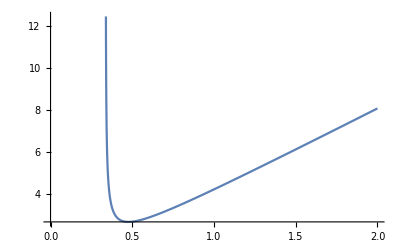

```mathematica
Plot[((30 Fr^2 π)/(√(7/5 (-5+18 Fr^2) lambda^2+(28 π^2)/3)))/.{lambda->4.716}, {Fr, 0,2}]
```

```mathematica
eta1N06Mod=eta1/.{n->3/5}//Simplify
eta3N06Mod=eta3/.{n->3/5,R->((3n+2)/2 ((2n+1)/n)^(n-2) cott)}//Simplify
```

-(5 cott)/3+550/171 (11/3)^(2/5) R

1/2 cott (2+1/n)^(-2+n) (2+3 n) (-(5382850 (11/3)^(2/5))/61047-(42350000 (11/3)^(1/5) cott^2 (2+1/n)^(2 (-2+n)) (2+3 n)^2)/1666737)+cott (2255/153+(41875 (11/3)^(4/5) cott^2 (2+1/n)^(2 (-2+n)) (2+3 n)^2)/9747)

```mathematica
amaDispn06=ao==√(-eta1N06Mod/eta3N06Mod)
```

ao==√(-(-(5 cott)/3+550/171 (11/3)^(2/5) R)/(1/2 cott (2+1/n)^(-2+n) (2+3 n) (-(5382850 (11/3)^(2/5))/61047-(42350000 (11/3)^(1/5) cott^2 (2+1/n)^(2 (-2+n)) (2+3 n)^2)/1666737)+cott (2255/153+(41875 (11/3)^(4/5) cott^2 (2+1/n)^(2 (-2+n)) (2+3 n)^2)/9747)))

```mathematica
amaDispPWLn06=amaDispn06//.{cott->(R/Fr^2 (n/(1+2n))^n), ao->(1/cott (2 π)/lambda)}//Simplify
```

(2 Fr^2 (n/(1+2 n))^-n π)/(lambda R)==√2 √(-(Fr^2 (n/(1+2 n))^-n (550/171 (11/3)^(2/5)-(5 (n/(1+2 n))^n)/(3 Fr^2)))/((2+1/n)^(-2+n) (2+3 n) (-(5382850 (11/3)^(2/5))/61047-(42350000 (11/3)^(1/5) (2+1/n)^(2 (-2+n)) (n/(1+2 n))^(2 n) (2+3 n)^2 R^2)/(1666737 Fr^4))+2 (2255/153+(41875 (11/3)^(4/5) (2+1/n)^(2 (-2+n)) (n/(1+2 n))^(2 n) (2+3 n)^2 R^2)/(9747 Fr^4))))

```mathematica
Solve[amaDispPWLn06, R]//FullSimplify
```

$Aborted

```mathematica
frVal=Table[i,{i,0.1,2.0,(2.0-0.10)/51}]
```

{0.1,0.137255,0.17451,0.211765,0.24902,0.286275,0.323529,0.360784,0.398039,0.435294,0.472549,0.509804,0.547059,0.584314,0.621569,0.658824,0.696078,0.733333,0.770588,0.807843,0.845098,0.882353,0.919608,0.956863,0.994118,1.03137,1.06863,1.10588,1.14314,1.18039,1.21765,1.2549,1.29216,1.32941,1.36667,1.40392,1.44118,1.47843,1.51569,1.55294,1.5902,1.62745,1.66471,1.70196,1.73922,1.77647,1.81373,1.85098,1.88824,1.92549,1.96275,2.}

```mathematica
reVal=Table[R/.NSolve[amaDispPWLn06/.{Fr-> frVal[[i]] , lambda->4.716, n->3/5},R,PositiveReals][[1]],{i,1,Length[frVal]}]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{R/.{}⟦1⟧,R/.{}⟦1⟧,2.55118,1.59332,1.56644,1.64985,1.77103,1.91008,2.05913,2.21441,2.37387,2.53627,2.70084,2.86707,3.03457,3.2031,3.37246,3.5425,3.71311,3.88421,4.05571,4.22756,4.39971,4.57214,4.74479,4.91765,5.09069,5.2639,5.43725,5.61073,5.78434,5.95805,6.13185,6.30575,6.47972,6.65378,6.8279,7.00208,7.17632,7.35062,7.52496,7.69936,7.87379,8.04827,8.22278,8.39733,8.57192,8.74653,8.92117,9.09584,9.27054,9.44526}

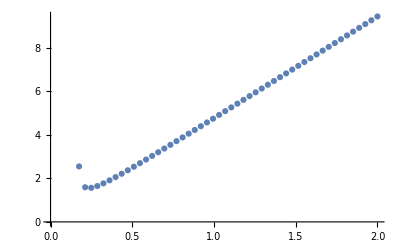

```mathematica
data=Transpose@{frVal,reVal};
ListPlot[data]
```

```mathematica
eta1N04Mod=eta1/.{n->2/5}//Simplify
eta3N04Mod=eta3/.{n->2/5,R->((3n+2)/2 ((2n+1)/n)^(n-2) cott)}//Simplify
```

-(5 cott)/2+(675 3^(1/5) R)/(32 2^(3/5))

1/1525415936 45 cott (15 6^(1/5) (2+1/n)^(-2+n) (2+3 n) (340891648 2^(1/5)-296764875 3^(2/5) cott^2 (2+1/n)^(2 (-2+n)) (2+3 n)^2)+704 (-1083392+1796375 2^(4/5) 3^(2/5) cott^2 (2+1/n)^(2 (-2+n)) (2+3 n)^2))

```mathematica
amaDispn04=ao==√(-eta1N04Mod/eta3N04Mod)
```

ao==11776/3 √(11/5) √(-((-(5 cott)/2+(675 3^(1/5) R)/(32 2^(3/5)))/(cott (15 6^(1/5) (2+1/n)^(-2+n) (2+3 n) (340891648 2^(1/5)-296764875 3^(2/5) cott^2 (2+1/n)^(2 (-2+n)) (2+3 n)^2)+704 (-1083392+1796375 2^(4/5) 3^(2/5) cott^2 (2+1/n)^(2 (-2+n)) (2+3 n)^2)))))

```mathematica
amaDispPWLn04=amaDispn04//.{cott->(R/Fr^2 (n/(1+2n))^n), ao->(1/cott (2 π)/lambda)}//Simplify
```

(2 Fr^2 (n/(1+2 n))^-n π)/(lambda R)==1472/3 √11 √(-((Fr^2 (n/(1+2 n))^-n (135 2^(2/5) 3^(1/5)-(32 (n/(1+2 n))^n)/Fr^2))/(15 6^(1/5) (2+1/n)^(-2+n) (2+3 n) (340891648 2^(1/5)-(296764875 3^(2/5) (2+1/n)^(2 (-2+n)) (n/(1+2 n))^(2 n) (2+3 n)^2 R^2)/Fr^4)+704 (-1083392+(1796375 2^(4/5) 3^(2/5) (2+1/n)^(2 (-2+n)) (n/(1+2 n))^(2 n) (2+3 n)^2 R^2)/Fr^4))))

```mathematica
frVal=Table[i,{i,0.1,2.0,(2.0-0.10)/91}]
```

{0.1,0.120879,0.141758,0.162637,0.183516,0.204396,0.225275,0.246154,0.267033,0.287912,0.308791,0.32967,0.350549,0.371429,0.392308,0.413187,0.434066,0.454945,0.475824,0.496703,0.517582,0.538462,0.559341,0.58022,0.601099,0.621978,0.642857,0.663736,0.684615,0.705495,0.726374,0.747253,0.768132,0.789011,0.80989,0.830769,0.851648,0.872527,0.893407,0.914286,0.935165,0.956044,0.976923,0.997802,1.01868,1.03956,1.06044,1.08132,1.1022,1.12308,1.14396,1.16484,1.18571,1.20659,1.22747,1.24835,1.26923,1.29011,1.31099,1.33187,1.35275,1.37363,1.39451,1.41538,1.43626,1.45714,1.47802,1.4989,1.51978,1.54066,1.56154,1.58242,1.6033,1.62418,1.64505,1.66593,1.68681,1.70769,1.72857,1.74945,1.77033,1.79121,1.81209,1.83297,1.85385,1.87473,1.8956,1.91648,1.93736,1.95824,1.97912,2.}

```mathematica
reVal2=Table[R/.NSolve[amaDispPWLn04/.{Fr-> frVal[[i]] , lambda->4.716, n->2/5},R,PositiveReals][[1]],{i,1,Length[frVal]}]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧,R/.{}⟦1⟧}